# Cosmomathica

Adrian Vollmer, Institute for theoretical Physics, Universität Heidelberg, 2013

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
<<(NotebookDirectory[]<>"interface.m")
```

A short description for all functions

```mathematica
?Transfer
```

Transfer[omegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function. It takes the reduced total matter density ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function...

```mathematica
?Halofit
```

Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: ...) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.

```mathematica
?CosmicEmu
```

CosmicEmu[omegaM, omegaB, sigma8, ns, w] provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as ...

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes Ω_C, ..., as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

### Transfer

This is how you call Eisenstein&Hu’s Transfer function code

```mathematica
tfdata=Transfer[.12,.3,2.7,.67];
```

To see what kind of data has been returned, type this

```mathematica
tfdata/.Rule[lhs_,rhs_]->lhs
```

{Transfer[soundhorizon],Transfer[peak],Transfer[kvalues],Transfer[full],Transfer[baryon],Transfer[cdm],Transfer[nowiggles],Transfer[zerobaryons]}

To access it, use the replacement rules, e.g. for the sound horizon

```mathematica
Transfer["soundhorizon"]/.tfdata
```

134.385

or for the various transfer functions

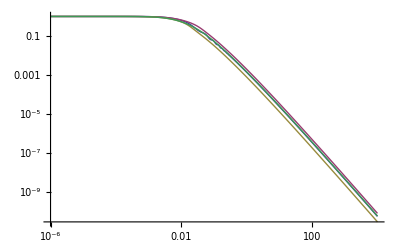

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Transfer["kvalues"]/.tfdata,pk}],{pk,{
Transfer["full"],
Transfer["cdm"],
Transfer["nowiggles"],
Transfer["zerobaryons"]
}/.tfdata}],Joined->True]
```

### Halofit

Call the Halofit+ code

```mathematica
hfdata=Halofit[.25,.75,.259,.8,.9,1.,1.5];
```

View the output data options

```mathematica
hfdata/.Rule[lhs_,rhs_]->lhs
```

{Halofit[avalues],Halofit[kvalues],Halofit[ellvalues],Halofit[kappaBBKS],Halofit[BBKS],Halofit[kappaPD96],Halofit[PD96],Halofit[kappaHalofit],Halofit[Halofit]}

Plot the matter power spectrum using the Halofit algorithm at different redshifts

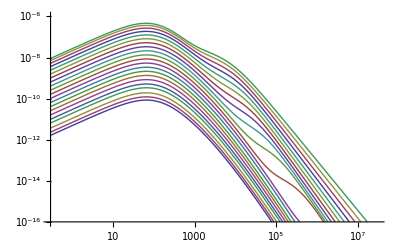

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["kvalues"]/.hfdata,pk}],
{pk,Halofit["Halofit"]/.hfdata}],
Joined->True,PlotRange->{1*^-16,1*^-6}]
```

Note that Halofit[“Halofit”] returns a list of lists, each of which corresponds to the power spectrum at a different redshift or scale factor. The scale factors are as follows

```mathematica
Halofit["avalues"]/.hfdata
```

{0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.}

Plot the convergence power spectrum using three different algorithms

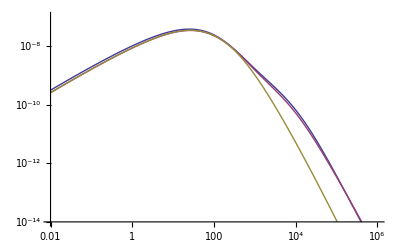

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["ellvalues"]/.hfdata,kappa}],{kappa,{
Halofit["kappaHalofit"],
Halofit["kappaPD96"],
Halofit["kappaBBKS"]
}/.hfdata}],Joined->True,PlotRange->{1*^-14,1*^-7}]
```

### Cosmic Emulator

Call the Cosmic Emulator

```mathematica
cedata=CosmicEmu[.15,.022,.9,.9,-1];
```

View the output

```mathematica
cedata/.Rule[lhs_,rhs_]->lhs
```

{CosmicEmu[zvalues],CosmicEmu[pk],CosmicEmu[soundhorizon],CosmicEmu[zlastscatter],CosmicEmu[dlss],CosmicEmu[hubblecmb]}

Redshift of last scattering

```mathematica
CosmicEmu["zlastscatter"]/.cedata
```

1093.05

Power spectrum at the following redshifts

```mathematica
CosmicEmu["zvalues"]/.cedata
```

{1.,0.666667,0.428571,0.25,0.111111,0.}

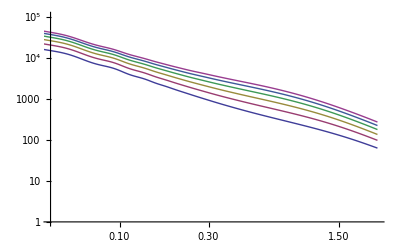

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,CosmicEmu["pk"]/.cedata}],Joined->True]
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options:

```mathematica
Options[CAMB]
```

{Tcmb→2.7255,OmegaNu→0,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→none,WantCMB→True,WantTransfer→True,WantCls→True,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,TransferHighPrecision→False,WantScalars→True,WantVectors→True,WantTensors→True,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→3000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→0.9,TransferKperLogInt→0,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→True,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves, see the CAMB readme for further information) with the transfer function for two different redshifts

```mathematica
cambdata=CAMB[.2,.05,.75,.67,-1.,WantTransfer->True,DoLensing->False,TransferRedshifts->{1.5,0.}];
```

```mathematica
cambdata/.Rule[lhs_,rhs_]->lhs
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[CLvector],CAMB[CLtensor],CAMB[PSlinear1],CAMB[PSnonlinear1],CAMB[Transfer1],CAMB[ints],CAMB[floats]}

Age of the universe:

```mathematica
CAMB["age"]/.cambdata
```

14.7873

Plot the scalar angular power spectrum

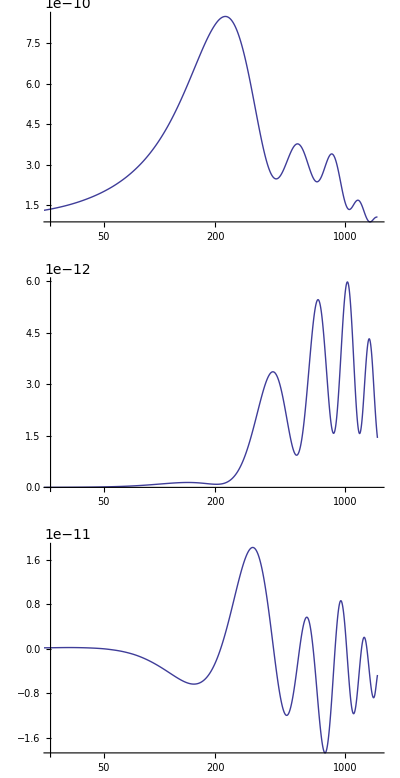

```mathematica
GraphicsGrid@Transpose@List@Table[ListLogLinearPlot[plot,Joined->True,PlotRange->All],{plot,CAMB["CLscalar"]/.cambdata}]
```

Plot the linear and nonlinear matter power spectrum for the both redshifts

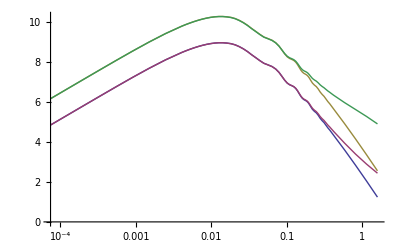

```mathematica
ListLogLinearPlot[{CAMB["PSlinear1"],CAMB["PSnonlinear1"],CAMB["PSlinear2"],CAMB["PSnonlinear2"]}/.cambdata,Joined->True]
```

Plot the CDM transfer function at the first redshift

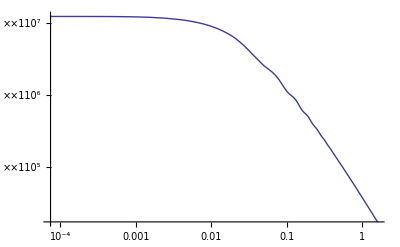

```mathematica
ListLogLogPlot[(CAMB["Transfer1"]/.cambdata)[[All,{1,2}]],Joined->True]
```